# Markov process for Lineages

## h=0

Sampling inter-division times

```mathematica
Clear[γ]
f[m_, s_] := (γ*(m + s^(-1))*Exp[γ*m*(1 - s)])/s^γ
```

```mathematica
(* Check *)
Integrate[f[2,q],{q,1,Infinity}]
```

1

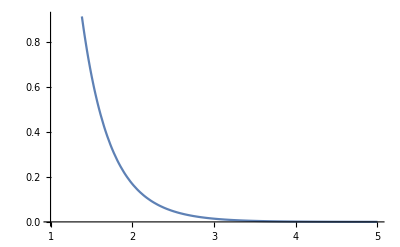

```mathematica
Plot[f[2,q],{q,1,5}]
```

```mathematica
(* Generate lineage of sizes at birth (M) *)
n=1000;
m=1;
S=ConstantArray[0,n];
M=ConstantArray[0,n];
For[i=1,i<n+1,i++,
s=RandomVariate[ProbabilityDistribution[f[m,q],{q,1,Infinity}],1][[1]];
S[[i]]=s;
m=m*s/2;
M[[i]]=m
]
```

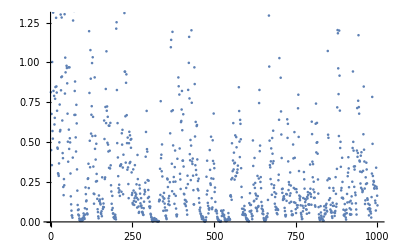

```mathematica
ListPlot[M]
```

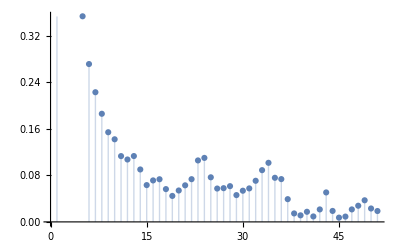

```mathematica
ListPlot[CorrelationFunction[M,{50}],Filling->0]
```

Sampling sizes at birth from PDF

```mathematica
(* Probability distribution for size at birth Markov process *)
Clear[γ]
F[m_,mp_]:=2^(1-γ)*γ*(mp/m)^γ*(1+(1/(2*m)))*Exp[γ(mp-2*m)]
```

```mathematica
(* Check *)
Integrate[F[q,mp],{q,mp/2,Infinity}]
```

ConditionalExpression[1,Re[γ]>0&&((Im[mp]==0&&Re[mp]>0)||mp∉Reals)]

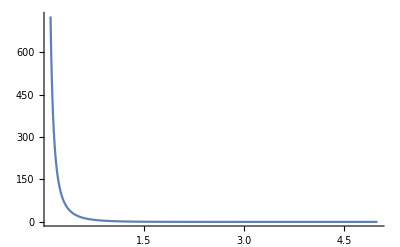

```mathematica
γ=1.0;
Plot[F[m,2],{m,0.1,5},PlotRange->All]
```

```mathematica
n=1000;
γ=1.;
m=1;
Mnc=ConstantArray[0,n];
For[i=1,i<n+1,i++,
m=RandomVariate[ProbabilityDistribution[F[q,m],{q,m/2,Infinity}],1][[1]];
Mnc[[i]]=m
]
```

```mathematica
ListPlot[Mnc,PlotRange->All]
```

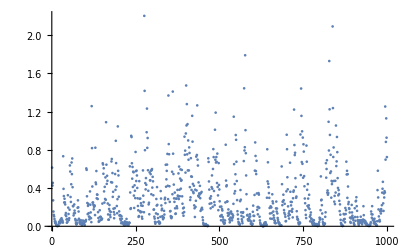
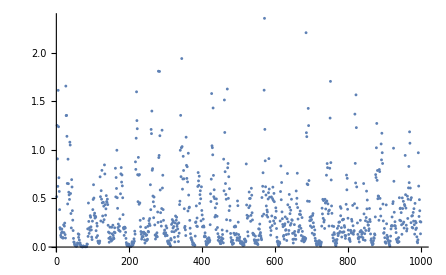

```mathematica
ListPlot[CorrelationFunction[Mnc,{50}],Filling->0]
```

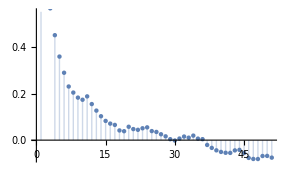
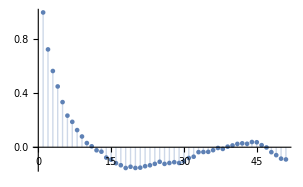

Sampling sizes at birth from PDF in log space (slow)

```mathematica
Clear[γ]
F[x_,xp_]:=2^(-γ)*γ*Exp[γ*(-x+xp+Exp[xp]-2*Exp[x])+Log[1+2*Exp[x]]]
```

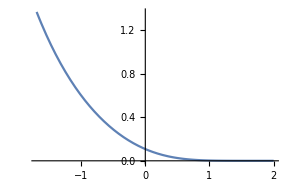

```mathematica
γ=1.0;
Plot[F[x,-1],{x,-1-Log[2],2},PlotRange->All]
```

```mathematica
n=1000;
γ=1.;
x=Log[1];
Xnc=ConstantArray[0,n];
For[i=1,i<n+1,i++,
x=RandomVariate[ProbabilityDistribution[F[q,x],{q,x-Log[2],Infinity}],1][[1]];
Xnc[[i]]=x
]
```

$Aborted

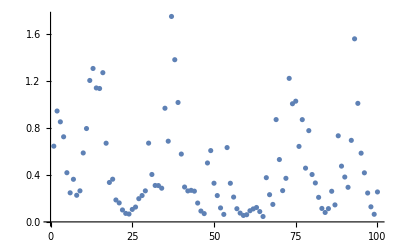

```mathematica
ListPlot[Exp[Xnc],PlotRange->All]
```

Sampling sizes at birth using inverse CDF in log space (fast)

```mathematica
Integrate[F[q,xp],{q,xp-Log[2],x},Assumptions->{γ>0}]
```

1-2^-γ ⅇ^((-2 ⅇ^x+ⅇ^xp-x+xp) γ)

```mathematica
Clear[γ]
intF[x_,xp_]:=1-2^-γ ⅇ^((-2 ⅇ^x+ⅇ^xp-x+xp) γ)
```

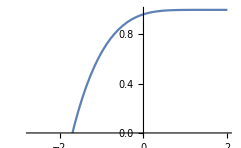

```mathematica
γ=1.0;
Plot[intF[x,-1],{x,-2-Log[2],2},PlotRange->{0,1}]
```

```mathematica
n=50000;
γ=1.0;
x=Log[1.];
X=ConstantArray[0,n];
For[i=1,i<n+1,i++,
x=(q/.Solve[intF[q,x]==RandomVariate[UniformDistribution[],1][[1]]])[[1]];
X[[i]]=x;
(*If[Mod[i,n/10]==0,Print[Mean[M[[1;;i]]]]]*)
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

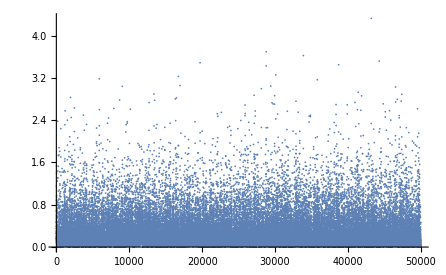

```mathematica
ListPlot[Exp[X], PlotRange->All]
```

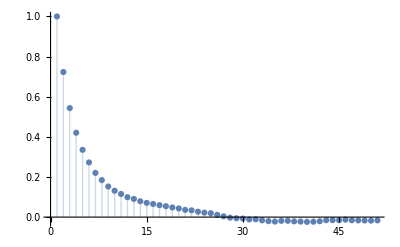

```mathematica
ListPlot[CorrelationFunction[Exp[X],{50}],Filling->0,PlotRange->All]
```

```mathematica
corr=CorrelationFunction[Exp[X],{1, 25}];
logcorr = Log[corr];
```

```mathematica
Clear[x]
lm = LinearModelFit[logcorr,x,x]
```

FittedModel[-0.532752-0.145274 x]

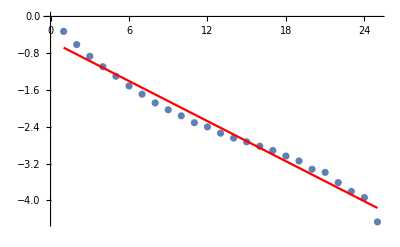

```mathematica
Show[ListPlot[Log[corr]],Plot[lm[x],{x,1,25},PlotStyle->Red]]
```

## h>0

Sampling from PDF

```mathematica
Clear[γ,h]
F[m_,mp_]:=γ*((1+2*m)/(m+h/2))*((2*m+h)/(mp+h))^(γ*(h-1))*Exp[-γ*(2*m-mp)]
```

```mathematica
Simplify[Integrate[F[q,mp],{q,mp/2,Infinity},Assumptions->{γ>0,h>0,mp>0}]]
```

1

```mathematica
n=100;
γ=1.0;
h=0.1;
m=h;
M=ConstantArray[0,n];
For[i=1,i<n+1,i++,
m=RandomVariate[ProbabilityDistribution[F[q,m],{q,m/2,Infinity}],1][[1]];
M[[i]]=m;
(*If[Mod[i,n/10]==0,Print[Mean[M[[1;;i]]]]]*)
]
```

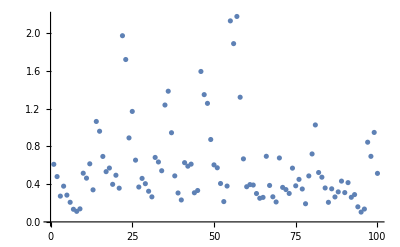

```mathematica
ListPlot[M,PlotRange->All]
```

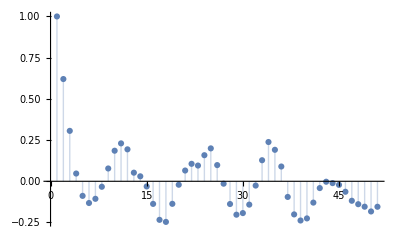

```mathematica
ListPlot[CorrelationFunction[M,{50}],Filling->0,PlotRange->All]
```

Sampling with inverse CDF

```mathematica
Clear[γ,h]
F[x_,xp_]:=2*γ*Exp[x+γ*(Exp[xp]-2*Exp[x])+(γ*(h-1)-1)*Log[2*Exp[x]+h]+Log[1+2*Exp[x]]-γ*(h-1)*Log[h+Exp[xp]]]
```

```mathematica
Integrate[F[q,xp],{q,xp-Log[2],x},Assumptions->{γ>0,h>0,h<1}]
```

ConditionalExpression[1-ⅇ^((-2 ⅇ^x+ⅇ^xp) γ) ((2 ⅇ^x+h)/(ⅇ^xp+h))^((-1+h) γ),2 ⅇ^x+h≥0&&ⅇ^xp+h≥0]

```mathematica
intF[x_,xp_]:=1-ⅇ^((-2 ⅇ^x+ⅇ^xp) γ) (2 ⅇ^x+h)^((-1+h) γ) (ⅇ^xp+h)^(γ-h γ)
```

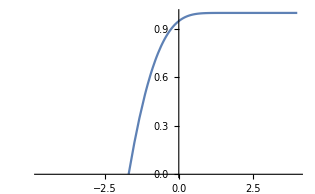

```mathematica
γ=1.0;
h=0.1;
Plot[intF[x,-1],{x,-4-Log[2],4},PlotRange->{0,1}]
```

```mathematica
n=100;
γ=1.0;
h=0.1;
x=Log[h];
X=ConstantArray[0,n];
For[i=1,i<n+1,i++,
x=(q/.Solve[intF[q,x]==RandomVariate[UniformDistribution[],1][[1]]])[[1]];
X[[i]]=x;
(*If[Mod[i,n/10]==0,Print[Mean[M[[1;;i]]]]]*)
]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve :: ifun will be suppressed during this calculation.

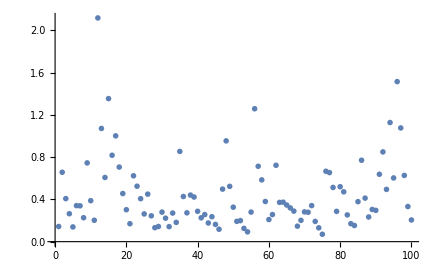

```mathematica
ListPlot[Exp[X], PlotRange->All]
```

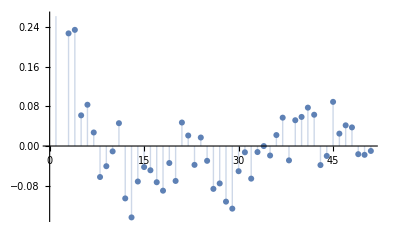

```mathematica
p1=ListPlot[CorrelationFunction[Exp[X],{50}],Filling->0]
```